```mathematica
distro0 = {{0, 1}, {1, 2}, {2, 5},{3, 8}, {4, 5}, {5, 2}}
```

{{0,1},{1,2},{2,5},{3,8},{4,5},{5,2}}

```mathematica
distro0=Import["/home/sam/Documents/School/rm/vpong/", "FieldSeparators"->"\t"];
```

```mathematica
simpleData[distro_]:=Module[{rv},
rv = {};
Do[
rv=Join[rv, Table[datum[[1]], {i, datum[[2]]}]];
,{datum, distro}
];
rv];
normalize[distro_]:=Table[{datum[[1]], datum[[2]]/Length[simpleData[distro]]},{datum,distro}];
```

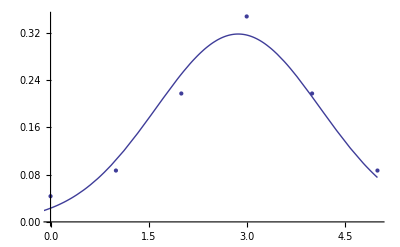

```mathematica
distroPlot =ListPlot[normalize[distro0]];
simple = simpleData[distro0];
mean = Mean[simple];
stdev = StandardDeviation[simple];
ndPlot =Plot[PDF[NormalDistribution[mean, stdev], x],{x,-5,5} ];
Show[distroPlot, ndPlot]
```

```mathematica
PearsonChiSquareTest[distro0]
```